```mathematica
(*Quit[];*)
```

```mathematica
On[Assert];
```

## Embedding Icosahedron and Geodesic Lengths

```mathematica
TOLARCCOS=1.0*10^-14;
TOLSTRICT=1.0*10^-14;
TOLLOOSE=1.0*10^-12;
TOLSLOPPY=1.0*10^-6;
EPSNUMERICALDERIVATIVE=1.0*10^-8;
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/nobuyukimatsumoto/Dropbox/0_BU/qed3

```mathematica
nrefine=2;

PtsIcosahedron3P=Chop[Import["vertex_coordinates_n"<>ToString[nrefine]<>".dat"][[2;;]]];

PtsIcosahedron1P=Permute[#,{3,1,2}]&/@PtsIcosahedron3P;
PtsIcosahedron2P=Permute[#,{2,3,1}]&/@PtsIcosahedron3P;
PtsIcosahedron1M={#[[1]],-#[[2]],-#[[3]]}&/@PtsIcosahedron1P;
PtsIcosahedron2M={#[[1]],-#[[2]],-#[[3]]}&/@PtsIcosahedron2P;
PtsIcosahedron3M={#[[1]],-#[[2]],-#[[3]]}&/@PtsIcosahedron3P;
```

## Get owners

```mathematica
IsRange[{x_,y_,z_}]:=(Abs[z]<1&&y>=0);

SitesInside1P=IsRange[#]&/@PtsIcosahedron1P;
SitesInside2P=IsRange[#]&/@PtsIcosahedron2P;
SitesInside3P=IsRange[#]&/@PtsIcosahedron3P;

SitesInside1M=IsRange[#]&/@PtsIcosahedron1M;
SitesInside2M=IsRange[#]&/@PtsIcosahedron2M;
SitesInside3M=IsRange[#]&/@PtsIcosahedron3M;

SitesInsideTables=<|"1+"->SitesInside1P
,"1-"->SitesInside1M
,"2+"->SitesInside2P
,"2-"->SitesInside2M
,"3+"->SitesInside3P
,"3-"->SitesInside3M
|>;
PtsIcosahedronTables=<|"1+"->PtsIcosahedron1P
,"1-"->PtsIcosahedron1M
,"2+"->PtsIcosahedron2P
,"2-"->PtsIcosahedron2M
,"3+"->PtsIcosahedron3P
,"3-"->PtsIcosahedron3M
|>;
```

```mathematica
ArcCosWrapper[x_]:=Module[{},
If[Abs[x+1]<TOLARCCOS
,
Return[-Pi]
,
If[Abs[x-1]<TOLARCCOS
,
Return[0]
,
Return[ArcCos[x]]
];
];
];
```

```mathematica
GetRowNumbers[list_,pattern_]:=Module[
{tmp,sel},
tmp={Range[Length[list]],list}//Transpose;
sel=Select[tmp,#[[2]]==pattern&];
Return[Transpose[sel][[1]]];
];

GetRowNumbersValue[list_,value_]:=Module[
{tmp,sel},
tmp={Range[Length[list]],list}//Transpose;
sel=Select[tmp,Abs[N[#[[2]]]-value]<TOLSTRICT&];
Return[Transpose[sel][[1]]];
];

NPts=PtsIcosahedron1P//Length;

Embedding3D[{θ_,ϕ_}]:={Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}

ProjectionS2[{x_,y_,z_}]:=Module[{r,θ,ϕ},
r=Sqrt[x*x+y*y+z*z];
θ=ArcCosWrapper[z/r];
If[
θ!=0&&θ!=Pi,
ϕ=ArcCosWrapper[x/(r*Sin[θ])];
If[y<0,ϕ*=-1]];
Return[{θ,ϕ}]
]

GeodesicLength[x1_,x2_]:=ArcCosWrapper[x1.x2];
```

```mathematica
DistanceTable=Table[
GeodesicLength[PtsIcosahedron3P[[i]],PtsIcosahedron3P[[j]]],
{i,1,NPts},{j,1,NPts}
];

Select[Flatten[Abs[DistanceTable]],#>10^-2&];
distances=Sort[DeleteDuplicates[%,Abs[#1-#2]<10^-12&]]

threshold=1.2*1.1071487177940904/nrefine(*(distances[[2]]+distances[[3]])/2*)
```

{0.553574,0.628319,1.01722,1.0472,1.10715,1.25664,1.5708,1.88496,2.03444,2.0944,2.12437,2.51327,2.58802,π}

0.664289

```mathematica
IsSingular[{x_,y_,z_},TOL_:TOLSTRICT]:=Module[
{P,res,norm},
norm=Norm[{x,y,z}];
If[norm<TOL,Return[True]];
P={x,y,z}/norm;
res=False;
If[Norm[P-{0.,0.,1.}]<TOL||Norm[P-{0.,0.,-1.}]<TOL,
res=True;
];
Return[res];
];
```

```mathematica
GetFacesInside[key_,lengthvalue_:threshold]:=Module[
{facelist,linklist,xinside,tmp,possibleFacesUndirected,ii,
facep,linksp,lensp,pts,isface,facesInside},

facelist={};
linklist={};

xinside=GetRowNumbers[SitesInsideTables[key],True];
tmp=Permutations[xinside,{3}];
possibleFacesUndirected=DeleteDuplicates[Sort[Sort[#]&/@tmp]];

For[ii=1,ii<=Length[possibleFacesUndirected],ii++,
facep=possibleFacesUndirected[[ii]];
linksp=DeleteDuplicates[Sort[Sort[#]&/@Permutations[facep,{2}]]];
pts=PtsIcosahedronTables[key];
lensp=GeodesicLength[pts[[#[[1]]]],pts[[#[[2]]]]]&/@linksp;
If[!AllTrue[IsSingular[pts[[#[[1]]]]+pts[[#[[2]]]]]&/@linksp,#==False&],Continue[]];
isface=AllTrue[(#<lengthvalue)&/@lensp,#==True&];
If[isface,
AppendTo[facelist,facep];
AppendTo[linklist,linksp];
];
];
Return[{facelist,Sort[DeleteDuplicates[Flatten[linklist,1]]]}];
];
```

```mathematica
NearestNeighborTable=Table[Transpose[Select[Transpose[{Range[NPts],DistanceTable[[i]]}],#[[2]]<threshold&]][[1]],{i,1,NPts}];

ppts=PtsIcosahedronTables["1+"];
Show[
Graphics3D[Sphere[{0,0,0},1]]
,Table[Graphics3D[{PointSize[0.05],Blue,Point[x]}],{x,ppts}]

,Graphics3D[{PointSize[0.05],Red,Point[Embedding3D[{0,0}]]}]
,Graphics3D[{PointSize[0.05],Green,Point[Embedding3D[{Pi,0}]]}]

,Graphics3D[{PointSize[0.05],Magenta,Point[ppts[[3]]]}]
,Graphics3D[{PointSize[0.05],Magenta,Point[ppts[[5]]]}]
]
```

-Graphics3D-

```mathematica
{FacesInside1P,LinksInside1P}=GetFacesInside["1+"];
{FacesInside2P,LinksInside2P}=GetFacesInside["2+"];
{FacesInside3P,LinksInside3P}=GetFacesInside["3+"];
{FacesInside1M,LinksInside1M}=GetFacesInside["1-"];
{FacesInside2M,LinksInside2M}=GetFacesInside["2-"];
{FacesInside3M,LinksInside3M}=GetFacesInside["3-"];

FacesInsideTables=<|"1+"->FacesInside1P
,"1-"->FacesInside1M
,"2+"->FacesInside2P
,"2-"->FacesInside2M
,"3+"->FacesInside3P
,"3-"->FacesInside3M
|>;

LinksInsideTables=<|"1+"->LinksInside1P
,"1-"->LinksInside1M
,"2+"->LinksInside2P
,"2-"->LinksInside2M
,"3+"->LinksInside3P
,"3-"->LinksInside3M
|>;
```

## Functions to Compute Geodesic Solutions

```mathematica
IsModdable[v_,q_,TOL_:TOLSTRICT]:=Mod[Norm[v],q]<TOL||Mod[-Norm[v],q]<TOL

GetCosϕ0[{θ1_,ϕ1_},{θ2_,ϕ2_},ι1_,ι2_]:=Module[{t12, res},
t12=Tan[θ1]/Tan[θ2];
res=ι2(t12 Cos[ϕ1]-ι1 Cos[ϕ2])/Sqrt[t12^2+1-ι1 2t12 Cos[ϕ1-ϕ2]];
Return[res]
];

Getϕ0[{θ1_,ϕ1_},{θ2_,ϕ2_},ι1_,ι2_]:=ArcCosWrapper[GetCosϕ0[{θ1,ϕ1},{θ2,ϕ2},ι1,ι2]];

CheckRatio[{θ1_,ϕ1_},{θ2_,ϕ2_},ι1_,ι2_,TOL_:TOLLOOSE]:=Module[
{ϕ0,ratio,bool},
ϕ0=Getϕ0[{θ1,ϕ1},{θ2,ϕ2},ι1,ι2];
ratio=ι1*Tan[θ1]Sin[ϕ1-ϕ0]/(Tan[θ2]Sin[ϕ2-ϕ0]);
bool=If[Abs[N[ratio]-1.0]<TOL,True,False];
Return[bool];
];

CheckSign[P_,Q_,eps1_:EPSNUMERICALDERIVATIVE]:=Module[{eps,deriv1F,deriv1B,deriv2F,deriv2B,deriv1,deriv2,sign1,sign2},
eps=eps1;
deriv1F=(ProjectionS2[P+eps*(Q-P)]-ProjectionS2[P])/eps;
deriv1B=-(ProjectionS2[P-eps*(Q-P)]-ProjectionS2[P])/eps;
While[
Abs[deriv1F[[1]]]<TOLSTRICT||Abs[deriv1B[[1]]]<TOLSTRICT,
eps=eps*2;
deriv1F=(ProjectionS2[P+eps*(Q-P)]-ProjectionS2[P])/eps;
deriv1B=-(ProjectionS2[P-eps*(Q-P)]-ProjectionS2[P])/eps;
];
If[Norm[deriv1F]<Norm[deriv1B],
deriv1=deriv1F,deriv1=deriv1B
];
eps=eps1;
While[
Abs[deriv1F[[2]]]<TOLSTRICT||Abs[deriv1B[[2]]]<TOLSTRICT,
eps=eps*2;
deriv1F=(ProjectionS2[P+eps*(Q-P)]-ProjectionS2[P])/eps;
deriv1B=-(ProjectionS2[P-eps*(Q-P)]-ProjectionS2[P])/eps;
];
If[Norm[deriv1F]<Norm[deriv1B],
deriv1[[2]]=deriv1F[[2]],deriv1[[2]]=deriv1B[[2]]
];

eps=eps1;
deriv2F=(ProjectionS2[Q+eps*(Q-P)]-ProjectionS2[Q])/eps;
deriv2B=-(ProjectionS2[Q-eps*(Q-P)]-ProjectionS2[Q])/eps;
While[
Abs[deriv2F[[1]]]<TOLSTRICT||Abs[deriv2B[[1]]]<TOLSTRICT,
eps=eps*2;
deriv2F=(ProjectionS2[Q+eps*(Q-P)]-ProjectionS2[Q])/eps;
deriv2B=-(ProjectionS2[Q-eps*(Q-P)]-ProjectionS2[Q])/eps;
];
If[Norm[deriv2F]<Norm[deriv2B],
deriv2=deriv2F,deriv2=deriv2B
];
eps=eps1;
While[
Abs[deriv2F[[2]]]<TOLSTRICT||Abs[deriv2B[[2]]]<TOLSTRICT,
eps=eps*2;
deriv2F=(ProjectionS2[Q+eps*(Q-P)]-ProjectionS2[Q])/eps;
deriv2B=-(ProjectionS2[Q-eps*(Q-P)]-ProjectionS2[Q])/eps;
];
If[Norm[deriv2F]<Norm[deriv2B],
deriv2[[2]]=deriv2F[[2]],deriv2[[2]]=deriv2B[[2]]
];

sign1=Sign[deriv1];
sign2=Sign[deriv2];

Return[{sign1,sign2}];
];
```

```mathematica
SolveGeodesicsConstPhi[{θ1_,ϕ1_},{θ2_,ϕ2_},P1_,P2_]:=Module[
{ell,θs,ϕs},
Assert[IsModdable[ϕ2-ϕ1,2Pi]];
ell=Abs[θ2-θ1];
(*k=0*)
θs[s_]:=θ1+(θ2-θ1)*s/ell;
ϕs[s_]:=ϕ1;
Return[{False,ell,{θs,ϕs}}];
]

SolveGeodesicsDeltaPhiEqPi[{θ1_,ϕ1_},{θ2_,ϕ2_},P1_,P2_]:=Module[
{ell,sN,sS,sE,θE,θs1,θs2,ϕs1,ϕs2},
Assert[Mod[ϕ2-ϕ1,2Pi,-Pi]==-Pi];
ell=GeodesicLength[P1,P2];
(*k=0*)
sN=GeodesicLength[P1,{0,0,1}];
sS=GeodesicLength[P2,{0,0,-1}];
If[sN<sS,
sE=sN;θE=0,
sE=sS;θE=Pi];
θs1[s_]:=θ1+(θE-θ1)*s/sE;
θs2[s_]:=θE+(θ2-θE)*(s-sE)/(ell-sE);
ϕs1[s_]:=ϕ1;
ϕs2[s_]:=ϕ2;
Return[{True,ell,sE,{θs1,ϕs1},{θs2,ϕs2}}];
]

SolveGeodesicsEndptEqPiHalf[{θ1_,ϕ1_},{θ2_,ϕ2_},P1_,P2_]:=Module[
{ell,ϕ0,ϕp,θp,s0,ιϕ,ιθ,absk,ϕsol,θsol},
ell=GeodesicLength[P1,P2];
(*If[θ1==Pi/2,*)
If[IsModdable[θ1-Pi/2,2Pi],
ϕ0=ϕ1;ϕp=ϕ2;θp=θ2;s0=0;
,
ϕ0=ϕ2;ϕp=ϕ1;θp=θ1;s0=ell;
];

ιϕ=Sign[Mod[ϕ2-ϕ1,2Pi,-Pi]];
ιθ=Sign[θ2-θ1];
absk=Sqrt[1/(1+1/(Tan[θp]^2 Sin[ϕp-ϕ0]^2))]//Simplify;

θsol[s_]:=ArcCos[-ιθ*Sqrt[1-absk^2]*Sin[s-s0]];
ϕsol[s_]:=ϕ0+ArcTan[ιϕ*absk*Tan[s-s0]];
Return[{False,ell,{θsol,ϕsol}}];

Assert[False];
]
```

```mathematica
SolveGeodesicsMonotonic[{θ1_,ϕ1_},{θ2_,ϕ2_},P1_,P2_]:=Module[
{sign1,sign2,ιϕ,ιθ,
ϕ0s,ϕ0,absk,ell,s0,ii,s0n,branch,
θsol,ϕsoltmp,diff1,diff2,diff3,ϕsol},
(*get ιθ,ιϕ*)
{sign1,sign2}=CheckSign[P1,P2];
Assert[sign1[[1]]==sign2[[1]]];
Assert[sign1[[2]]==sign2[[2]]];
ιϕ=sign1[[2]];
ιθ=sign1[[1]];
(*Get shape parameters*)
ϕ0s={};
If[CheckRatio[{θ1,ϕ1},{θ2,ϕ2},1,1],
ϕ0=Getϕ0[{θ1,ϕ1},{θ2,ϕ2},1,1];
ϕ0s=Append[ϕ0s,ϕ0];
];
If[CheckRatio[{θ1,ϕ1},{θ2,ϕ2},-1,1],
ϕ0=Getϕ0[{θ1,ϕ1},{θ2,ϕ2},-1,1];
ϕ0s=Append[ϕ0s,ϕ0];
];
If[CheckRatio[{θ1,ϕ1},{θ2,ϕ2},1,-1],
ϕ0=Getϕ0[{θ1,ϕ1},{θ2,ϕ2},1,-1];
ϕ0s=Append[ϕ0s,ϕ0];
];
If[CheckRatio[{θ1,ϕ1},{θ2,ϕ2},-1,-1],
ϕ0=Getϕ0[{θ1,ϕ1},{θ2,ϕ2},-1,-1];
ϕ0s=Append[ϕ0s,ϕ0];
];

For[ii=1,ii<=Length[ϕ0s],ii++,
ϕ0=ϕ0s[[ii]];
absk=Sqrt[1/(1+1/(Tan[θ1]^2 Sin[ϕ1-ϕ0]^2))];
(*adjust s0*)
ell=GeodesicLength[P1,P2];

For[branch=-1,branch<=1,branch++,
s0=-ArcTan[Tan[ϕ1-ϕ0]/(ιϕ absk)]+branch*Pi;

(*adjust branch of arctan*)
θsol[s_]:=ArcCos[-ιθ Sqrt[1-absk^2]Sin[s-s0]];
ϕsoltmp[s_]:=ϕ0+ArcTan[ιϕ absk Tan[s-s0]];

diff1=ϕsoltmp[0]-ϕ1;
diff2=θsol[ell]-θ2;

If[IsModdable[diff1,Pi]&&IsModdable[diff2,2Pi],
ϕsol[s_]:=ϕsoltmp[s]-diff1;

diff3=ϕsol[ell]-ϕ2;
If[!IsModdable[diff3,2Pi],Continue[]];

Return[{False,ell,{θsol,ϕsol}}]
];
];
];
Assert[False];
];
```

```mathematica
SolveGeodesicsAlteringιθ[{θ1_,ϕ1_},{θ2_,ϕ2_},P1_,P2_]:=Module[
{sign1,sign2,ιϕ,ιθ1,ιθ2,ii,
ϕ0,absk,ell,s01,s02,sE,ϕ0s,crit,
s01n,s02n,
branch1,branch2,branch3,branch4,
θsol1,θsol2,ϕsol1tmp,ϕsol2tmp,
diff1,diff2,diff3,diff4,
diff5,diff6,diff7,diff8,diff9,diff10,
ϕsol1,ϕsol2,θsol3,ϕsol3},
(*get ιθ,ιϕ*)
{sign1,sign2}=CheckSign[P1,P2];
Assert[sign1[[1]]==-sign2[[1]]];
Assert[sign1[[2]]==sign2[[2]]];
ιϕ=sign1[[2]];
ιθ1=sign1[[1]];
ιθ2=sign2[[1]];

(*Get shape parameters*)
ϕ0s={};
If[CheckRatio[{θ1,ϕ1},{θ2,ϕ2},1,1],
ϕ0=Getϕ0[{θ1,ϕ1},{θ2,ϕ2},1,1];
ϕ0s=Append[ϕ0s,ϕ0];
];
If[CheckRatio[{θ1,ϕ1},{θ2,ϕ2},-1,1],
ϕ0=Getϕ0[{θ1,ϕ1},{θ2,ϕ2},-1,1];
ϕ0s=Append[ϕ0s,ϕ0];
];
If[CheckRatio[{θ1,ϕ1},{θ2,ϕ2},1,-1],
ϕ0=Getϕ0[{θ1,ϕ1},{θ2,ϕ2},1,-1];
ϕ0s=Append[ϕ0s,ϕ0];
];
If[CheckRatio[{θ1,ϕ1},{θ2,ϕ2},-1,-1],
ϕ0=Getϕ0[{θ1,ϕ1},{θ2,ϕ2},-1,-1];
ϕ0s=Append[ϕ0s,ϕ0];
];

For[ii=1,ii<=Length[ϕ0s],ii++,
ϕ0=ϕ0s[[ii]];
absk=Sqrt[1/(1+1/(Tan[θ1]^2 Sin[ϕ1-ϕ0]^2))];
(*adjust s0*)
ell=GeodesicLength[P1,P2];

For[branch1=-3,branch1<=3,branch1++,
For[branch2=-3,branch2<=3,branch2++,
s01=-ArcTan[Tan[ϕ1-ϕ0]/(ιϕ absk)]+branch1*Pi;
s02=ell-ArcTan[Tan[ϕ2-ϕ0]/(ιϕ absk)]+branch2*Pi;

sE=Mod[s01+Pi/2,2Pi,-Pi];

(*adjust branch of arctan*)
θsol1[s_]:=ArcCos[-ιθ1 Sqrt[1-absk^2]Sin[s-s01]];
θsol2[s_]:=ArcCos[-ιθ2 Sqrt[1-absk^2]Sin[s-s02]];
ϕsol1tmp[s_]:=ϕ0+ArcTan[ιϕ absk Tan[s-s01]];
ϕsol2tmp[s_]:=ϕ0+ArcTan[ιϕ absk Tan[s-s02]];

diff1=ϕsol1tmp[0]-ϕ1;
diff2=ϕsol2tmp[ell]-ϕ2;

diff3=θsol1[0]-θ1;
diff4=θsol2[ell]-θ2;


crit=IsModdable[diff1,Pi]&&IsModdable[diff2,Pi]&&IsModdable[diff3,2Pi]&&IsModdable[diff4,2Pi];
If[crit,
ϕsol1[s_]:=ϕsol1tmp[s]-diff1;
ϕsol2[s_]:=ϕsol2tmp[s]-diff2;

diff5=ϕsol1[0]-ϕ1;
diff6=ϕsol2[ell]-ϕ2;
diff7=ϕsol1[sE]-ϕsol2[sE];
diff8=θsol1[0]-θ1;
diff9=θsol2[ell]-θ2;
diff10=θsol1[sE]-θsol2[sE];

If[!IsModdable[diff5,2Pi],Continue[]];
If[!IsModdable[diff6,2Pi],Continue[]];
If[!IsModdable[diff7,2Pi],Continue[]];
If[!IsModdable[diff8,2Pi],Continue[]];
If[!IsModdable[diff9,2Pi],Continue[]];
If[!IsModdable[diff10,2Pi],Continue[]];

If[IsModdable[sE,2Pi],
θsol3[s_]:=θsol2[s+sE];
ϕsol3[s_]:=ϕsol2[s+sE];

diff7=ϕsol3[0]-ϕ1;
diff8=θsol3[0]-θ1;
If[!IsModdable[diff7,2Pi],Continue[]];
If[!IsModdable[diff8,2Pi],Continue[]];

Return[{False,ell,{θsol3,ϕsol3}}]
,
If[IsModdable[ell-sE,2Pi],
θsol3[s_]:=θsol1[s-(ell-sE)];
ϕsol3[s_]:=ϕsol1[s-(ell-sE)];

diff7=ϕsol3[ell]-ϕ2;
diff8=θsol3[ell]-θ2;

diff7=ϕsol3[ell-TOLSTRICT]-ϕ2;
diff8=θsol3[ell-TOLSTRICT]-θ2;

If[!IsModdable[diff7,2Pi,TOLLOOSE],Continue[]];
If[!IsModdable[diff8,2Pi,TOLLOOSE],Continue[]];

Return[{False,ell-TOLSTRICT,{θsol3,ϕsol3}}]
,
Return[{True,ell,Mod[sE,2Pi,-Pi],{θsol1,ϕsol1},{θsol2,ϕsol2}}]
];
];
];
]];
];
Assert[False];
];
```

## Wrapper of the above functions

```mathematica
SolveGeodesics[{θ1_,ϕ1_},{θ2_,ϕ2_},P1_,P2_,verbose_:False]:=Module[
{sign1,sign2},

If[IsModdable[ϕ2-ϕ1,2Pi](*Mod[ϕ2-ϕ1,2Pi,-Pi]==0*)
,
If[verbose,Print["δϕ=0"]];
Return[SolveGeodesicsConstPhi[{θ1,ϕ1},{θ2,ϕ2},P1,P2]]
];

If[IsModdable[ϕ2-ϕ1+Pi,2Pi](*Mod[ϕ2-ϕ1,2Pi,-Pi]==-Pi*)
,
If[verbose,Print["δϕ=Pi"]];Return[SolveGeodesicsDeltaPhiEqPi[{θ1,ϕ1},{θ2,ϕ2},P1,P2]]
];

If[IsModdable[θ1-Pi/2,2Pi]||IsModdable[θ2-Pi/2,2Pi],
If[verbose,Print["θ1,2=Pi/2"]];Return[SolveGeodesicsEndptEqPiHalf[{θ1,ϕ1},{θ2,ϕ2},P1,P2]]
];

{sign1,sign2}=CheckSign[P1,P2];
Assert[sign1[[2]]==sign2[[2]]];

If[sign1[[1]]==sign2[[1]]
,
If[verbose,Print["Monotonic"]];
Return[SolveGeodesicsMonotonic[{θ1,ϕ1},{θ2,ϕ2},P1,P2]];
,
If[verbose,Print["Altering"]];
Return[SolveGeodesicsAlteringιθ[{θ1,ϕ1},{θ2,ϕ2},P1,P2]];
];
];
```

## Get Table of Solutions for Icosahedron

```mathematica
key="1+";
solutiontable={};

For[ell=1,ell<=Length[LinksInsideTables[key]],ell++,
Print[ell];
{i,j}=LinksInsideTables[key][[ell]];
P1=PtsIcosahedronTables[key][[i]];
P2=PtsIcosahedronTables[key][[j]];
{θ1,ϕ1}=ProjectionS2[P1];
{θ2,ϕ2}=ProjectionS2[P2];

If[(!IsModdable[ϕ1,2Pi])&&IsModdable[ϕ1,Pi]&&(!IsModdable[ϕ2,2Pi]),branch=Sign[ϕ2]Pi;];
If[(!IsModdable[ϕ2,2Pi])&&IsModdable[ϕ2,Pi]&&(!IsModdable[ϕ1,2Pi]),branch=Sign[ϕ1]Pi;];
sol=SolveGeodesics[{θ1,ϕ1},{θ2,ϕ2},P1,P2,True]//N;

If[sol[[1]]
,
Assert[IsModdable[{sol[[4]][[1]][0],sol[[4]][[2]][0]}-{θ1,ϕ1},2Pi]];
Assert[IsModdable[{sol[[5]][[1]][sol[[2]]],sol[[5]][[2]][sol[[2]]]}-{θ2,ϕ2},2Pi]];
,
Assert[IsModdable[{sol[[3]][[1]][0],sol[[3]][[2]][0]}-{θ1,ϕ1},2Pi]];
Assert[IsModdable[{sol[[3]][[1]][sol[[2]]],sol[[3]][[2]][sol[[2]]]}-{θ2,ϕ2},2Pi]];
];
AppendTo[solutiontable,sol];
];

SolutionTable1P=solutiontable;
```

1

θ1,2=Pi/2

2

θ1,2=Pi/2

3

δϕ=0

4

θ1,2=Pi/2

5

θ1,2=Pi/2

6

Monotonic

7

Monotonic

8

Monotonic

9

Monotonic

10

Monotonic

11

Monotonic

12

Monotonic

13

θ1,2=Pi/2

14

Monotonic

15

Monotonic

16

Monotonic

17

Altering

18

Monotonic

19

Monotonic

20

Monotonic

21

θ1,2=Pi/2

22

Monotonic

23

Monotonic

24

Monotonic

25

Monotonic

26

δϕ=0

27

Monotonic

28

Monotonic

29

Monotonic

30

Altering

31

Monotonic

32

Monotonic

33

Altering

34

Altering

35

Monotonic

36

Monotonic

37

Monotonic

38

Monotonic

39

Altering

40

Altering

41

Altering

42

Monotonic

43

Monotonic

44

Monotonic

45

Monotonic

46

Monotonic

47

Monotonic

48

Monotonic

49

Monotonic

50

θ1,2=Pi/2

51

Monotonic

52

θ1,2=Pi/2

53

Monotonic

54

Altering

55

Monotonic

56

δϕ=0

57

δϕ=0

58

δϕ=0

59

δϕ=0

60

δϕ=0

61

δϕ=0

62

δϕ=0

63

δϕ=0

```mathematica
plots1P={};
For[ii=1,ii<=Length[SolutionTable1P],ii++,
sol=SolutionTable1P[[ii]];
If[sol[[1]]==True,(*two solutions*)
{bool,ell,sE,{θsol1,ϕsol1},{θsol2,ϕsol2}}=sol;
AppendTo[plots1P,
{
ParametricPlot3D[Embedding3D[{θsol1[s],ϕsol1[s]}],{s,0,sE},PlotStyle->Magenta],
ParametricPlot3D[Embedding3D[{θsol2[s],ϕsol2[s]}],{s,sE,ell},PlotStyle->Cyan]
}
];
,
{bool,ell,{θsol,ϕsol}}=sol;
AppendTo[plots1P,
ParametricPlot3D[Embedding3D[{θsol[s],ϕsol[s]}],{s,0,ell},PlotStyle->Blue]
];
]];

Show[
Graphics3D[Sphere[{0,0,0},1]],
Graphics3D[{PointSize[0.05],Red,Point[Embedding3D[{0,0}]]}],
Graphics3D[{PointSize[0.05],Blue,Point[Embedding3D[{Pi,0}]]}],
plots1P
(*plots1P[[34]],*)
(*ParametricPlot3D[Embedding3D[{θsol1[s],ϕsol1[s]}],{s,0,sE},PlotStyle->Magenta],
ParametricPlot3D[Embedding3D[{θsol2[s],Pi+ϕsol2[s]}],{s,sE,ell},PlotStyle->Cyan]*)
]
```

-Graphics3D-

```mathematica
key="1-";
solutiontable={};

For[ell=1,ell<=Length[LinksInsideTables[key]],ell++,
Print[ell];
{i,j}=LinksInsideTables[key][[ell]];
P1=PtsIcosahedronTables[key][[i]];
P2=PtsIcosahedronTables[key][[j]];
{θ1,ϕ1}=ProjectionS2[P1];
{θ2,ϕ2}=ProjectionS2[P2];
If[(!IsModdable[ϕ1,2Pi])&&IsModdable[ϕ1,Pi]&&(!IsModdable[ϕ2,2Pi]),branch=Sign[ϕ2]Pi;];
If[(!IsModdable[ϕ2,2Pi])&&IsModdable[ϕ2,Pi]&&(!IsModdable[ϕ1,2Pi]),branch=Sign[ϕ1]Pi;];
sol=SolveGeodesics[{θ1,ϕ1},{θ2,ϕ2},P1,P2,True]//N;

If[sol[[1]]
,
Assert[IsModdable[{sol[[4]][[1]][0],sol[[4]][[2]][0]}-{θ1,ϕ1},2Pi]];
Assert[IsModdable[{sol[[5]][[1]][sol[[2]]],sol[[5]][[2]][sol[[2]]]}-{θ2,ϕ2},2Pi]];
,
Assert[IsModdable[{sol[[3]][[1]][0],sol[[3]][[2]][0]}-{θ1,ϕ1},2Pi]];
Assert[IsModdable[{sol[[3]][[1]][sol[[2]]],sol[[3]][[2]][sol[[2]]]}-{θ2,ϕ2},2Pi]];
];
AppendTo[solutiontable,sol];
];

SolutionTable1M=solutiontable;
```

1

Monotonic

2

δϕ=0

3

Altering

4

Altering

5

Monotonic

6

Monotonic

7

Monotonic

8

Monotonic

9

Monotonic

10

Altering

11

Monotonic

12

Monotonic

13

Monotonic

14

θ1,2=Pi/2

15

Monotonic

16

δϕ=0

17

Monotonic

18

Monotonic

19

θ1,2=Pi/2

20

Monotonic

21

Monotonic

22

θ1,2=Pi/2

23

θ1,2=Pi/2

24

θ1,2=Pi/2

25

δϕ=0

26

δϕ=0

27

Monotonic

28

δϕ=0

29

Altering

30

Monotonic

31

Monotonic

32

Monotonic

33

δϕ=0

34

Monotonic

35

θ1,2=Pi/2

36

Monotonic

37

Monotonic

38

Monotonic

39

Monotonic

40

Monotonic

41

θ1,2=Pi/2

42

Monotonic

43

Monotonic

44

Monotonic

45

Monotonic

46

Monotonic

47

Monotonic

48

Altering

49

δϕ=0

50

δϕ=0

51

δϕ=0

52

θ1,2=Pi/2

53

Monotonic

54

Monotonic

55

δϕ=0

56

Monotonic

57

Monotonic

58

Monotonic

59

Monotonic

60

Monotonic

61

Altering

62

Monotonic

63

Altering

```mathematica
plots1M={};
For[ii=1,ii<=Length[SolutionTable1M],ii++,
sol=SolutionTable1M[[ii]];
If[sol[[1]]==True,(*two solutions*)
{bool,ell,sE,{θsol1,ϕsol1},{θsol2,ϕsol2}}=sol;
AppendTo[plots1M,
{
ParametricPlot3D[Embedding3D[{θsol1[s],ϕsol1[s]}],{s,0,sE},PlotStyle->Magenta],
ParametricPlot3D[Embedding3D[{θsol2[s],ϕsol2[s]}],{s,sE,ell},PlotStyle->Cyan]
}
];
,
{bool,ell,{θsol,ϕsol}}=sol;
AppendTo[plots1M,
ParametricPlot3D[Embedding3D[{θsol[s],ϕsol[s]}],{s,0,ell},PlotStyle->Blue]
];
]]

Show[
Graphics3D[Sphere[{0,0,0},1]],
Graphics3D[{PointSize[0.05],Red,Point[Embedding3D[{0,0}]]}],
Graphics3D[{PointSize[0.05],Blue,Point[Embedding3D[{Pi,0}]]}],
plots1M
]
```

-Graphics3D-

```mathematica
key="2+";
solutiontable={};

For[ell=1,ell<=Length[LinksInsideTables[key]],ell++,
Print[ell];
{i,j}=LinksInsideTables[key][[ell]];
P1=PtsIcosahedronTables[key][[i]];
P2=PtsIcosahedronTables[key][[j]];
{θ1,ϕ1}=ProjectionS2[P1];
{θ2,ϕ2}=ProjectionS2[P2];
If[(!IsModdable[ϕ1,2Pi])&&IsModdable[ϕ1,Pi]&&(!IsModdable[ϕ2,2Pi]),branch=Sign[ϕ2]Pi;];
If[(!IsModdable[ϕ2,2Pi])&&IsModdable[ϕ2,Pi]&&(!IsModdable[ϕ1,2Pi]),branch=Sign[ϕ1]Pi;];
sol=SolveGeodesics[{θ1,ϕ1},{θ2,ϕ2},P1,P2,True]//N;

If[sol[[1]]
,
Assert[IsModdable[{sol[[4]][[1]][0],sol[[4]][[2]][0]}-{θ1,ϕ1},2Pi]];
Assert[IsModdable[{sol[[5]][[1]][sol[[2]]],sol[[5]][[2]][sol[[2]]]}-{θ2,ϕ2},2Pi]];
,
Assert[IsModdable[{sol[[3]][[1]][0],sol[[3]][[2]][0]}-{θ1,ϕ1},2Pi]];
Assert[IsModdable[{sol[[3]][[1]][sol[[2]]],sol[[3]][[2]][sol[[2]]]}-{θ2,ϕ2},2Pi]];
];
AppendTo[solutiontable,sol];
];

SolutionTable2P=solutiontable;
```

1

θ1,2=Pi/2

2

θ1,2=Pi/2

3

θ1,2=Pi/2

4

Monotonic

5

θ1,2=Pi/2

6

Altering

7

Monotonic

8

Altering

9

θ1,2=Pi/2

10

θ1,2=Pi/2

11

θ1,2=Pi/2

12

θ1,2=Pi/2

13

θ1,2=Pi/2

14

Monotonic

15

Monotonic

16

θ1,2=Pi/2

17

θ1,2=Pi/2

18

θ1,2=Pi/2

19

Monotonic

20

Altering

21

Monotonic

22

Altering

23

Monotonic

24

Monotonic

25

θ1,2=Pi/2

26

θ1,2=Pi/2

27

Monotonic

28

δϕ=0

29

Altering

30

Monotonic

31

Monotonic

32

δϕ=0

33

Monotonic

34

θ1,2=Pi/2

35

δϕ=0

36

δϕ=0

37

Monotonic

38

Altering

39

δϕ=0

40

Monotonic

41

Monotonic

42

δϕ=0

43

Monotonic

44

δϕ=0

45

θ1,2=Pi/2

46

δϕ=0

47

θ1,2=Pi/2

48

θ1,2=Pi/2

```mathematica
plots2P={};
For[ii=1,ii<=Length[SolutionTable2P],ii++,
sol=SolutionTable2P[[ii]];
If[sol[[1]]==True,(*two solutions*)
{bool,ell,sE,{θsol1,ϕsol1},{θsol2,ϕsol2}}=sol;
AppendTo[plots2P,
{
ParametricPlot3D[Embedding3D[{θsol1[s],ϕsol1[s]}],{s,0,sE},PlotStyle->Magenta],
ParametricPlot3D[Embedding3D[{θsol2[s],ϕsol2[s]}],{s,sE,ell},PlotStyle->Cyan]
}
];
,
{bool,ell,{θsol,ϕsol}}=sol;
AppendTo[plots2P,
ParametricPlot3D[Embedding3D[{θsol[s],ϕsol[s]}],{s,0,ell},PlotStyle->Blue]
];
]]

Show[
Graphics3D[Sphere[{0,0,0},1]],
Graphics3D[{PointSize[0.05],Red,Point[Embedding3D[{0,0}]]}],
Graphics3D[{PointSize[0.05],Blue,Point[Embedding3D[{Pi,0}]]}],
plots2P
]
```

-Graphics3D-

```mathematica
key="2-";
solutiontable={};

For[ell=1,ell<=Length[LinksInsideTables[key]],ell++,
Print[ell];
{i,j}=LinksInsideTables[key][[ell]];
P1=PtsIcosahedronTables[key][[i]];
P2=PtsIcosahedronTables[key][[j]];
{θ1,ϕ1}=ProjectionS2[P1];
{θ2,ϕ2}=ProjectionS2[P2];
If[(!IsModdable[ϕ1,2Pi])&&IsModdable[ϕ1,Pi]&&(!IsModdable[ϕ2,2Pi]),branch=Sign[ϕ2]Pi;];
If[(!IsModdable[ϕ2,2Pi])&&IsModdable[ϕ2,Pi]&&(!IsModdable[ϕ1,2Pi]),branch=Sign[ϕ1]Pi;];
sol=SolveGeodesics[{θ1,ϕ1},{θ2,ϕ2},P1,P2,True]//N;

If[sol[[1]]
,
Assert[IsModdable[{sol[[4]][[1]][0],sol[[4]][[2]][0]}-{θ1,ϕ1},2Pi]];
Assert[IsModdable[{sol[[5]][[1]][sol[[2]]],sol[[5]][[2]][sol[[2]]]}-{θ2,ϕ2},2Pi]];
,
Assert[IsModdable[{sol[[3]][[1]][0],sol[[3]][[2]][0]}-{θ1,ϕ1},2Pi]];
Assert[IsModdable[{sol[[3]][[1]][sol[[2]]],sol[[3]][[2]][sol[[2]]]}-{θ2,ϕ2},2Pi]];
];
AppendTo[solutiontable,sol];
];

SolutionTable2M=solutiontable;
```

1

θ1,2=Pi/2

2

θ1,2=Pi/2

3

δϕ=0

4

Monotonic

5

δϕ=0

6

θ1,2=Pi/2

7

Monotonic

8

Altering

9

δϕ=0

10

Monotonic

11

Monotonic

12

θ1,2=Pi/2

13

Monotonic

14

δϕ=0

15

δϕ=0

16

θ1,2=Pi/2

17

θ1,2=Pi/2

18

Monotonic

19

Monotonic

20

Monotonic

21

Altering

22

θ1,2=Pi/2

23

θ1,2=Pi/2

24

θ1,2=Pi/2

25

θ1,2=Pi/2

26

θ1,2=Pi/2

27

Monotonic

28

θ1,2=Pi/2

29

Altering

30

Monotonic

31

Monotonic

32

Monotonic

33

Altering

34

θ1,2=Pi/2

35

θ1,2=Pi/2

36

θ1,2=Pi/2

37

θ1,2=Pi/2

38

θ1,2=Pi/2

39

θ1,2=Pi/2

40

δϕ=0

41

δϕ=0

42

Monotonic

43

δϕ=0

44

Monotonic

45

Monotonic

46

Altering

47

Altering

48

Monotonic

```mathematica
plots2M={};
For[ii=1,ii<=Length[SolutionTable2M],ii++,
sol=SolutionTable2M[[ii]];
If[sol[[1]]==True,(*two solutions*)
{bool,ell,sE,{θsol1,ϕsol1},{θsol2,ϕsol2}}=sol;
AppendTo[plots2M,
{
ParametricPlot3D[Embedding3D[{θsol1[s],ϕsol1[s]}],{s,0,sE},PlotStyle->Magenta],
ParametricPlot3D[Embedding3D[{θsol2[s],ϕsol2[s]}],{s,sE,ell},PlotStyle->Cyan]
}
];
,
{bool,ell,{θsol,ϕsol}}=sol;
AppendTo[plots2M,
ParametricPlot3D[Embedding3D[{θsol[s],ϕsol[s]}],{s,0,ell},PlotStyle->Blue]
];
]]

Show[
Graphics3D[Sphere[{0,0,0},1]],
Graphics3D[{PointSize[0.05],Red,Point[Embedding3D[{0,0}]]}],
Graphics3D[{PointSize[0.05],Blue,Point[Embedding3D[{Pi,0}]]}],
plots2M
]
```

-Graphics3D-

```mathematica
key="3+";
solutiontable={};

For[ell=1,ell<=Length[LinksInsideTables[key]],ell++,
Print[ell];
{i,j}=LinksInsideTables[key][[ell]];
P1=PtsIcosahedronTables[key][[i]];
P2=PtsIcosahedronTables[key][[j]];
{θ1,ϕ1}=ProjectionS2[P1];
{θ2,ϕ2}=ProjectionS2[P2];
If[(!IsModdable[ϕ1,2Pi])&&IsModdable[ϕ1,Pi]&&(!IsModdable[ϕ2,2Pi]),branch=Sign[ϕ2]Pi;];
If[(!IsModdable[ϕ2,2Pi])&&IsModdable[ϕ2,Pi]&&(!IsModdable[ϕ1,2Pi]),branch=Sign[ϕ1]Pi;];
sol=SolveGeodesics[{θ1,ϕ1},{θ2,ϕ2},P1,P2,True]//N;

If[sol[[1]]
,
Assert[IsModdable[{sol[[4]][[1]][0],sol[[4]][[2]][0]}-{θ1,ϕ1},2Pi]];
Assert[IsModdable[{sol[[5]][[1]][sol[[2]]],sol[[5]][[2]][sol[[2]]]}-{θ2,ϕ2},2Pi,TOLLOOSE]];
,
Assert[IsModdable[{sol[[3]][[1]][0],sol[[3]][[2]][0]}-{θ1,ϕ1},2Pi]];
Assert[IsModdable[{sol[[3]][[1]][sol[[2]]],sol[[3]][[2]][sol[[2]]]}-{θ2,ϕ2},2Pi,TOLLOOSE]];
];
AppendTo[solutiontable,sol];
];

SolutionTable3P=solutiontable;
```

1

δϕ=0

2

Altering

3

Monotonic

4

Altering

5

Monotonic

6

Altering

7

Altering

8

θ1,2=Pi/2

9

θ1,2=Pi/2

10

Monotonic

11

δϕ=0

12

Monotonic

13

Altering

14

θ1,2=Pi/2

15

θ1,2=Pi/2

16

Monotonic

17

θ1,2=Pi/2

18

θ1,2=Pi/2

19

Monotonic

20

δϕ=0

21

Altering

22

θ1,2=Pi/2

23

θ1,2=Pi/2

24

θ1,2=Pi/2

25

θ1,2=Pi/2

26

δϕ=0

27

θ1,2=Pi/2

28

Altering

29

Monotonic

30

Altering

31

θ1,2=Pi/2

32

θ1,2=Pi/2

33

θ1,2=Pi/2

34

Altering

35

Monotonic

36

θ1,2=Pi/2

37

θ1,2=Pi/2

38

δϕ=0

39

θ1,2=Pi/2

40

Altering

41

Monotonic

42

Altering

43

θ1,2=Pi/2

44

θ1,2=Pi/2

45

θ1,2=Pi/2

46

θ1,2=Pi/2

47

θ1,2=Pi/2

48

Altering

49

θ1,2=Pi/2

50

Monotonic

51

δϕ=0

52

Monotonic

53

θ1,2=Pi/2

54

Monotonic

```mathematica
plots3P={};
For[ii=1,ii<=Length[SolutionTable3P],ii++,
sol=SolutionTable3P[[ii]];
If[sol[[1]]==True,(*two solutions*)
{bool,ell,sE,{θsol1,ϕsol1},{θsol2,ϕsol2}}=sol;
AppendTo[plots3P,
{
ParametricPlot3D[Embedding3D[{θsol1[s],ϕsol1[s]}],{s,0,sE},PlotStyle->Magenta],
ParametricPlot3D[Embedding3D[{θsol2[s],ϕsol2[s]}],{s,sE,ell},PlotStyle->Cyan]
}
];
,
{bool,ell,{θsol,ϕsol}}=sol;
AppendTo[plots3P,
ParametricPlot3D[Embedding3D[{θsol[s],ϕsol[s]}],{s,0,ell},PlotStyle->Blue]
];
]]

Show[
Graphics3D[Sphere[{0,0,0},1]],
Graphics3D[{PointSize[0.05],Red,Point[Embedding3D[{0,0}]]}],
Graphics3D[{PointSize[0.05],Blue,Point[Embedding3D[{Pi,0}]]}],
plots3P
]
```

-Graphics3D-

```mathematica
key="3-";
solutiontable={};

For[ell=1,ell<=Length[LinksInsideTables[key]],ell++,
Print[ell];
{i,j}=LinksInsideTables[key][[ell]];
P1=PtsIcosahedronTables[key][[i]];
P2=PtsIcosahedronTables[key][[j]];
{θ1,ϕ1}=ProjectionS2[P1];
{θ2,ϕ2}=ProjectionS2[P2];
If[(!IsModdable[ϕ1,2Pi])&&IsModdable[ϕ1,Pi]&&(!IsModdable[ϕ2,2Pi]),branch=Sign[ϕ2]Pi;];
If[(!IsModdable[ϕ2,2Pi])&&IsModdable[ϕ2,Pi]&&(!IsModdable[ϕ1,2Pi]),branch=Sign[ϕ1]Pi;];
sol=SolveGeodesics[{θ1,ϕ1},{θ2,ϕ2},P1,P2,True]//N;

If[sol[[1]]
,
Assert[IsModdable[{sol[[4]][[1]][0],sol[[4]][[2]][0]}-{θ1,ϕ1},2Pi]];
Assert[IsModdable[{sol[[5]][[1]][sol[[2]]],sol[[5]][[2]][sol[[2]]]}-{θ2,ϕ2},2Pi,TOLLOOSE]];
,
Assert[IsModdable[{sol[[3]][[1]][0],sol[[3]][[2]][0]}-{θ1,ϕ1},2Pi]];
Assert[IsModdable[{sol[[3]][[1]][sol[[2]]],sol[[3]][[2]][sol[[2]]]}-{θ2,ϕ2},2Pi,TOLLOOSE]];
];
AppendTo[solutiontable,sol];
];

SolutionTable3M=solutiontable;
```

1

δϕ=0

2

Altering

3

Monotonic

4

Altering

5

θ1,2=Pi/2

6

Monotonic

7

δϕ=0

8

Altering

9

Monotonic

10

Monotonic

11

θ1,2=Pi/2

12

Altering

13

θ1,2=Pi/2

14

θ1,2=Pi/2

15

Monotonic

16

δϕ=0

17

Monotonic

18

Altering

19

θ1,2=Pi/2

20

θ1,2=Pi/2

21

Altering

22

θ1,2=Pi/2

23

θ1,2=Pi/2

24

θ1,2=Pi/2

25

θ1,2=Pi/2

26

Altering

27

δϕ=0

28

θ1,2=Pi/2

29

Altering

30

Monotonic

31

Monotonic

32

θ1,2=Pi/2

33

θ1,2=Pi/2

34

δϕ=0

35

θ1,2=Pi/2

36

Altering

37

θ1,2=Pi/2

38

Altering

39

Monotonic

40

Altering

41

θ1,2=Pi/2

42

θ1,2=Pi/2

43

Altering

44

Monotonic

45

θ1,2=Pi/2

46

θ1,2=Pi/2

47

δϕ=0

48

θ1,2=Pi/2

49

Monotonic

50

θ1,2=Pi/2

51

Monotonic

52

θ1,2=Pi/2

53

θ1,2=Pi/2

54

θ1,2=Pi/2

```mathematica
plots3M={};
For[ii=1,ii<=Length[SolutionTable3M],ii++,
sol=SolutionTable3M[[ii]];
If[sol[[1]]==True,(*two solutions*)
{bool,ell,sE,{θsol1,ϕsol1},{θsol2,ϕsol2}}=sol;
AppendTo[plots3M,
{
ParametricPlot3D[Embedding3D[{θsol1[s],ϕsol1[s]}],{s,0,sE},PlotStyle->Magenta],
ParametricPlot3D[Embedding3D[{θsol2[s],ϕsol2[s]}],{s,sE,ell},PlotStyle->Cyan]
}
];
,
{bool,ell,{θsol,ϕsol}}=sol;
AppendTo[plots3M,
ParametricPlot3D[Embedding3D[{θsol[s],ϕsol[s]}],{s,0,ell},PlotStyle->Blue]
];
]]

Show[
Graphics3D[Sphere[{0,0,0},1]],
Graphics3D[{PointSize[0.05],Red,Point[Embedding3D[{0,0}]]}],
Graphics3D[{PointSize[0.05],Blue,Point[Embedding3D[{Pi,0}]]}],
plots3M,
ParametricPlot3D[Embedding3D[{θsol1[s],ϕsol1[s]}],{s,0,sE},PlotStyle->Magenta]
(*,ParametricPlot3D[Embedding3D[{θsol2[s],ϕsol2[s]}],{s,sE,ell},PlotStyle->Cyan]*)
]
```

-Graphics3D-

```mathematica
SolutionTables=<|"1+"->SolutionTable1P
,"1-"->SolutionTable1M
,"2+"->SolutionTable2P
,"2-"->SolutionTable2M
,"3+"->SolutionTable3P
,"3-"->SolutionTable3M
|>;

AllLinks={};
AllLinks=Join[AllLinks,LinksInsideTables["1+"]];
AllLinks=Join[AllLinks,LinksInsideTables["2+"]];
AllLinks=Join[AllLinks,LinksInsideTables["3+"]];
AllLinks=Join[AllLinks,LinksInsideTables["1-"]];
AllLinks=Join[AllLinks,LinksInsideTables["2-"]];
AllLinks=Join[AllLinks,LinksInsideTables["3-"]];
AllLinks=Sort[DeleteDuplicates[AllLinks]];

list={};
list=Join[list,{#[[1]],#[[2]],#[[3]],"1+",#[[4]]}&/@Transpose[{LinksInside1P,#[[-1]]&/@SolutionTable1P,#[[1]]&/@SolutionTable1P,Range[Length[SolutionTable1P]]}]];
list=Join[list,{#[[1]],#[[2]],#[[3]],"2+",#[[4]]}&/@Transpose[{LinksInside2P,#[[-1]]&/@SolutionTable2P,#[[1]]&/@SolutionTable2P,Range[Length[SolutionTable2P]]}]];
list=Join[list,{#[[1]],#[[2]],#[[3]],"3+",#[[4]]}&/@Transpose[{LinksInside3P,#[[-1]]&/@SolutionTable3P,#[[1]]&/@SolutionTable3P,Range[Length[SolutionTable3P]]}]];
list=Join[list,{#[[1]],#[[2]],#[[3]],"1-",#[[4]]}&/@Transpose[{LinksInside1M,#[[-1]]&/@SolutionTable1M,#[[1]]&/@SolutionTable1M,Range[Length[SolutionTable1M]]}]];
list=Join[list,{#[[1]],#[[2]],#[[3]],"2-",#[[4]]}&/@Transpose[{LinksInside2M,#[[-1]]&/@SolutionTable2M,#[[1]]&/@SolutionTable2M,Range[Length[SolutionTable2M]]}]];
list=Join[list,{#[[1]],#[[2]],#[[3]],"3-",#[[4]]}&/@Transpose[{LinksInside3M,#[[-1]]&/@SolutionTable3M,#[[1]]&/@SolutionTable3M,Range[Length[SolutionTable3M]]}]];
(*chosenLabel=Select[list,(#[[2]]==True&&#[[3]]==False)&];*)

chosenLabel=Select[list,(#[[2]]==True)&];
SolutionChosen={#[[4]],#[[5]],#[[1]],SolutionTables[#[[4]]][[#[[5]]]]}&/@chosenLabel;
SolutionChosenNoDuplicate=DeleteDuplicates[SolutionChosen,#1[[3]]==#2[[3]]&];
Length[AllLinks]==Length[SolutionChosenNoDuplicate];
```

## ω_yz factors

```mathematica
GetOmegaN[SolutionSet_]:=Module[
{bool,ell,sE,θsol1,ϕsol1,θsol2,ϕsol2,θsol,ϕsol,int1,int2,int},
If[SolutionSet[[1]],
{bool,ell,sE,{θsol1,ϕsol1},{θsol2,ϕsol2}}=SolutionSet;
integrand1[s_]=FullSimplify[D[ϕsol1[s],s]Cos[θsol1[s]]];
int1=NIntegrate[integrand1[s],{s,0.,sE}];
integrand2[s_]=FullSimplify[D[ϕsol2[s],s]Cos[θsol2[s]]];
int2=NIntegrate[integrand2[s],{s,sE,ell}];

Return[int1+int2];
,
{bool,ell,{θsol,ϕsol}}=SolutionSet;
integrand[s_]=FullSimplify[D[ϕsol[s],s]Cos[θsol[s]]];
int=NIntegrate[integrand[s],{s,0.,ell}];
Return[int];
]
];
```

```mathematica
keys={"1+","2+","3+","1-","2-","3-"};
```

```mathematica
OmegaTables=<||>;
Do[
Print[key];
linktab=LinksInsideTables[key];
soltab=SolutionTables[key];
AppendTo[OmegaTables,key->Map[{key,linktab[[#]],GetOmegaN[soltab[[#]]]}&,Range[Length[soltab]]]];
,
{key,keys}]
```

1+

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

2+

3+

1-

2-

3-

## e_yz and alpha

```mathematica
SignWrapper[x_]:=If[x==0,1,Sign[x]];
```

```mathematica
alphas1P={};
For[i=1,i<=Length[SolutionTable1P],i++,
soltest=SolutionTable1P[[i]];
ell=soltest[[2]];
(*Print["i=",i];*)

If[soltest[[1]],
θ1=soltest[[4,1]][0];
dθds1=D[soltest[[4,1]][s],s]/.{s->0};
dϕds1=D[soltest[[4,2]][s],s]/.{s->0};
Assert[Abs[dθds1^2+Sin[θ1]^2 dϕds1^2-1.0]<TOLSLOPPY];

e1={dθds1,Sin[θ1]dϕds1};
α1=Mod[SignWrapper[e1[[2]]]ArcCos[e1[[1]]],2Pi,-Pi];
(*Print[Norm[Cos[α1]-e1[[1]]]+Norm[Sin[α1]-e1[[2]]]];*)
Assert[Norm[Cos[α1]-e1[[1]]]+Norm[Sin[α1]-e1[[2]]]<TOLSLOPPY];

θ2=soltest[[5,1]][ell];
dθds2=D[soltest[[5,1]][s],s]/.{s->ell};
dϕds2=D[soltest[[5,2]][s],s]/.{s->ell};
Assert[Abs[dθds2^2+Sin[θ2]^2 dϕds2^2-1.0]<TOLSLOPPY];

e2={dθds2,Sin[θ2]dϕds2};
α2=Mod[SignWrapper[e2[[2]]]ArcCos[e2[[1]]],2Pi,-Pi];
(*Print[Norm[Cos[α2]-e2[[1]]]+Norm[Sin[α2]-e2[[2]]]];*)
Assert[Norm[Cos[α2]-e2[[1]]]+Norm[Sin[α2]-e2[[2]]]<TOLSLOPPY];
,
θ1=soltest[[3,1]][0];
dθds1=D[soltest[[3,1]][s],s]/.{s->0};
dϕds1=D[soltest[[3,2]][s],s]/.{s->0};
Assert[Abs[dθds1^2+Sin[θ1]^2 dϕds1^2-1.0]<TOLLOOSE];

e1={dθds1,Sin[θ1]dϕds1};
α1=Mod[SignWrapper[e1[[2]]]ArcCos[e1[[1]]],2Pi,-Pi];
(*Print[Norm[Cos[α1]-e1[[1]]]+Norm[Sin[α1]-e1[[2]]]];*)
Assert[Norm[Cos[α1]-e1[[1]]]+Norm[Sin[α1]-e1[[2]]]<TOLSLOPPY];

θ2=soltest[[3,1]][ell];
dθds2=D[soltest[[3,1]][s],s]/.{s->ell};
dϕds2=D[soltest[[3,2]][s],s]/.{s->ell};
Assert[Abs[dθds2^2+Sin[θ2]^2 dϕds2^2-1.0]<TOLSLOPPY];

e2={dθds2,Sin[θ2]dϕds2};
α2=Mod[SignWrapper[e2[[2]]]ArcCos[e2[[1]]],2Pi,-Pi];
(*Print[Norm[Cos[α2]-e2[[1]]]+Norm[Sin[α2]-e2[[2]]]];*)
Assert[Norm[Cos[α2]-e2[[1]]]+Norm[Sin[α2]-e2[[2]]]<TOLSLOPPY];
](*end if*);
(*Print[α1, ", ", α2 ];*)
AppendTo[alphas1P,{α1,α2}];
](*end for*);
```

```mathematica
alphas1M={};
For[i=1,i<=Length[SolutionTable1M],i++,
soltest=SolutionTable1M[[i]];
ell=soltest[[2]];
(*Print["i=",i];*)

If[soltest[[1]],
θ1=soltest[[4,1]][0];
dθds1=D[soltest[[4,1]][s],s]/.{s->0};
dϕds1=D[soltest[[4,2]][s],s]/.{s->0};
Assert[Abs[dθds1^2+Sin[θ1]^2 dϕds1^2-1.0]<TOLSLOPPY];

e1={dθds1,Sin[θ1]dϕds1};
α1=Mod[SignWrapper[e1[[2]]]ArcCos[e1[[1]]],2Pi,-Pi];
(*Print[Norm[Cos[α1]-e1[[1]]]+Norm[Sin[α1]-e1[[2]]]];*)
Assert[Norm[Cos[α1]-e1[[1]]]+Norm[Sin[α1]-e1[[2]]]<TOLSLOPPY];

θ2=soltest[[5,1]][ell];
dθds2=D[soltest[[5,1]][s],s]/.{s->ell};
dϕds2=D[soltest[[5,2]][s],s]/.{s->ell};
Assert[Abs[dθds2^2+Sin[θ2]^2 dϕds2^2-1.0]<TOLSLOPPY];

e2={dθds2,Sin[θ2]dϕds2};
α2=Mod[SignWrapper[e2[[2]]]ArcCos[e2[[1]]],2Pi,-Pi];
(*Print[Norm[Cos[α2]-e2[[1]]]+Norm[Sin[α2]-e2[[2]]]];*)
Assert[Norm[Cos[α2]-e2[[1]]]+Norm[Sin[α2]-e2[[2]]]<TOLSLOPPY];
,
θ1=soltest[[3,1]][0];
dθds1=D[soltest[[3,1]][s],s]/.{s->0};
dϕds1=D[soltest[[3,2]][s],s]/.{s->0};
Assert[Abs[dθds1^2+Sin[θ1]^2 dϕds1^2-1.0]<TOLLOOSE];

e1={dθds1,Sin[θ1]dϕds1};
α1=Mod[SignWrapper[e1[[2]]]ArcCos[e1[[1]]],2Pi,-Pi];
(*Print[Norm[Cos[α1]-e1[[1]]]+Norm[Sin[α1]-e1[[2]]]];*)
Assert[Norm[Cos[α1]-e1[[1]]]+Norm[Sin[α1]-e1[[2]]]<TOLSLOPPY];

θ2=soltest[[3,1]][ell];
dθds2=D[soltest[[3,1]][s],s]/.{s->ell};
dϕds2=D[soltest[[3,2]][s],s]/.{s->ell};
Assert[Abs[dθds2^2+Sin[θ2]^2 dϕds2^2-1.0]<TOLSLOPPY];

e2={dθds2,Sin[θ2]dϕds2};
α2=Mod[SignWrapper[e2[[2]]]ArcCos[e2[[1]]],2Pi,-Pi];
(*Print[Norm[Cos[α2]-e2[[1]]]+Norm[Sin[α2]-e2[[2]]]];*)
Assert[Norm[Cos[α2]-e2[[1]]]+Norm[Sin[α2]-e2[[2]]]<TOLSLOPPY];
](*end if*);
(*Print[α1, ", ", α2 ];*)
AppendTo[alphas1M,{α1,α2}];
](*end for*);
```

```mathematica
alphas2P={};
For[i=1,i<=Length[SolutionTable2P],i++,
soltest=SolutionTable2P[[i]];
ell=soltest[[2]];
(*Print["i=",i];*)

If[soltest[[1]],
θ1=soltest[[4,1]][0];
dθds1=D[soltest[[4,1]][s],s]/.{s->0};
dϕds1=D[soltest[[4,2]][s],s]/.{s->0};
Assert[Abs[dθds1^2+Sin[θ1]^2 dϕds1^2-1.0]<TOLSLOPPY];

e1={dθds1,Sin[θ1]dϕds1};
α1=Mod[SignWrapper[e1[[2]]]ArcCos[e1[[1]]],2Pi,-Pi];
(*Print[Norm[Cos[α1]-e1[[1]]]+Norm[Sin[α1]-e1[[2]]]];*)
Assert[Norm[Cos[α1]-e1[[1]]]+Norm[Sin[α1]-e1[[2]]]<TOLSLOPPY];

θ2=soltest[[5,1]][ell];
dθds2=D[soltest[[5,1]][s],s]/.{s->ell};
dϕds2=D[soltest[[5,2]][s],s]/.{s->ell};
Assert[Abs[dθds2^2+Sin[θ2]^2 dϕds2^2-1.0]<TOLSLOPPY];

e2={dθds2,Sin[θ2]dϕds2};
α2=Mod[SignWrapper[e2[[2]]]ArcCos[e2[[1]]],2Pi,-Pi];
(*Print[Norm[Cos[α2]-e2[[1]]]+Norm[Sin[α2]-e2[[2]]]];*)
Assert[Norm[Cos[α2]-e2[[1]]]+Norm[Sin[α2]-e2[[2]]]<TOLSLOPPY];
,
θ1=soltest[[3,1]][0];
dθds1=D[soltest[[3,1]][s],s]/.{s->0};
dϕds1=D[soltest[[3,2]][s],s]/.{s->0};
Assert[Abs[dθds1^2+Sin[θ1]^2 dϕds1^2-1.0]<TOLLOOSE];

e1={dθds1,Sin[θ1]dϕds1};
α1=Mod[SignWrapper[e1[[2]]]ArcCos[e1[[1]]],2Pi,-Pi];
(*Print[Norm[Cos[α1]-e1[[1]]]+Norm[Sin[α1]-e1[[2]]]];*)
Assert[Norm[Cos[α1]-e1[[1]]]+Norm[Sin[α1]-e1[[2]]]<TOLSLOPPY];

θ2=soltest[[3,1]][ell];
dθds2=D[soltest[[3,1]][s],s]/.{s->ell};
dϕds2=D[soltest[[3,2]][s],s]/.{s->ell};
Assert[Abs[dθds2^2+Sin[θ2]^2 dϕds2^2-1.0]<TOLSLOPPY];

e2={dθds2,Sin[θ2]dϕds2};
α2=Mod[SignWrapper[e2[[2]]]ArcCos[e2[[1]]],2Pi,-Pi];
(*Print[Norm[Cos[α2]-e2[[1]]]+Norm[Sin[α2]-e2[[2]]]];*)
Assert[Norm[Cos[α2]-e2[[1]]]+Norm[Sin[α2]-e2[[2]]]<TOLSLOPPY];
](*end if*);
(*Print[α1, ", ", α2 ];*)
AppendTo[alphas2P,{α1,α2}];
](*end for*);
```

```mathematica
alphas2M={};
For[i=1,i<=Length[SolutionTable2M],i++,
soltest=SolutionTable2M[[i]];
ell=soltest[[2]];
(*Print["i=",i];*)

If[soltest[[1]],
θ1=soltest[[4,1]][0];
dθds1=D[soltest[[4,1]][s],s]/.{s->0};
dϕds1=D[soltest[[4,2]][s],s]/.{s->0};
Assert[Abs[dθds1^2+Sin[θ1]^2 dϕds1^2-1.0]<TOLSLOPPY];

e1={dθds1,Sin[θ1]dϕds1};
α1=Mod[SignWrapper[e1[[2]]]ArcCos[e1[[1]]],2Pi,-Pi];
(*Print[Norm[Cos[α1]-e1[[1]]]+Norm[Sin[α1]-e1[[2]]]];*)
Assert[Norm[Cos[α1]-e1[[1]]]+Norm[Sin[α1]-e1[[2]]]<TOLSLOPPY];

θ2=soltest[[5,1]][ell];
dθds2=D[soltest[[5,1]][s],s]/.{s->ell};
dϕds2=D[soltest[[5,2]][s],s]/.{s->ell};
Assert[Abs[dθds2^2+Sin[θ2]^2 dϕds2^2-1.0]<TOLSLOPPY];

e2={dθds2,Sin[θ2]dϕds2};
α2=Mod[SignWrapper[e2[[2]]]ArcCos[e2[[1]]],2Pi,-Pi];
(*Print[Norm[Cos[α2]-e2[[1]]]+Norm[Sin[α2]-e2[[2]]]];*)
Assert[Norm[Cos[α2]-e2[[1]]]+Norm[Sin[α2]-e2[[2]]]<TOLSLOPPY];
,
θ1=soltest[[3,1]][0];
dθds1=D[soltest[[3,1]][s],s]/.{s->0};
dϕds1=D[soltest[[3,2]][s],s]/.{s->0};
Assert[Abs[dθds1^2+Sin[θ1]^2 dϕds1^2-1.0]<TOLLOOSE];

e1={dθds1,Sin[θ1]dϕds1};
α1=Mod[SignWrapper[e1[[2]]]ArcCos[e1[[1]]],2Pi,-Pi];
(*Print[Norm[Cos[α1]-e1[[1]]]+Norm[Sin[α1]-e1[[2]]]];*)
Assert[Norm[Cos[α1]-e1[[1]]]+Norm[Sin[α1]-e1[[2]]]<TOLSLOPPY];

θ2=soltest[[3,1]][ell];
dθds2=D[soltest[[3,1]][s],s]/.{s->ell};
dϕds2=D[soltest[[3,2]][s],s]/.{s->ell};
Assert[Abs[dθds2^2+Sin[θ2]^2 dϕds2^2-1.0]<TOLSLOPPY];

e2={dθds2,Sin[θ2]dϕds2};
α2=Mod[SignWrapper[e2[[2]]]ArcCos[e2[[1]]],2Pi,-Pi];
(*Print[Norm[Cos[α2]-e2[[1]]]+Norm[Sin[α2]-e2[[2]]]];*)
Assert[Norm[Cos[α2]-e2[[1]]]+Norm[Sin[α2]-e2[[2]]]<TOLSLOPPY];
](*end if*);
(*Print[α1, ", ", α2 ];*)
AppendTo[alphas2M,{α1,α2}];
](*end for*);
```

```mathematica
alphas3P={};
For[i=1,i<=Length[SolutionTable3P],i++,
soltest=SolutionTable3P[[i]];
ell=soltest[[2]];
(*Print["i=",i];*)

If[soltest[[1]],
θ1=soltest[[4,1]][0];
dθds1=D[soltest[[4,1]][s],s]/.{s->0};
dϕds1=D[soltest[[4,2]][s],s]/.{s->0};
Assert[Abs[dθds1^2+Sin[θ1]^2 dϕds1^2-1.0]<TOLSLOPPY];

e1={dθds1,Sin[θ1]dϕds1};
α1=Mod[SignWrapper[e1[[2]]]ArcCos[e1[[1]]],2Pi,-Pi];
(*Print[Norm[Cos[α1]-e1[[1]]]+Norm[Sin[α1]-e1[[2]]]];*)
Assert[Norm[Cos[α1]-e1[[1]]]+Norm[Sin[α1]-e1[[2]]]<TOLSLOPPY];

θ2=soltest[[5,1]][ell];
dθds2=D[soltest[[5,1]][s],s]/.{s->ell};
dϕds2=D[soltest[[5,2]][s],s]/.{s->ell};
Assert[Abs[dθds2^2+Sin[θ2]^2 dϕds2^2-1.0]<TOLSLOPPY];

e2={dθds2,Sin[θ2]dϕds2};
α2=Mod[SignWrapper[e2[[2]]]ArcCos[e2[[1]]],2Pi,-Pi];
(*Print[Norm[Cos[α2]-e2[[1]]]+Norm[Sin[α2]-e2[[2]]]];*)
Assert[Norm[Cos[α2]-e2[[1]]]+Norm[Sin[α2]-e2[[2]]]<TOLSLOPPY];
,
θ1=soltest[[3,1]][0];
dθds1=D[soltest[[3,1]][s],s]/.{s->0};
dϕds1=D[soltest[[3,2]][s],s]/.{s->0};
Assert[Abs[dθds1^2+Sin[θ1]^2 dϕds1^2-1.0]<TOLLOOSE];

e1={dθds1,Sin[θ1]dϕds1};
α1=Mod[SignWrapper[e1[[2]]]ArcCos[e1[[1]]],2Pi,-Pi];
(*Print[Norm[Cos[α1]-e1[[1]]]+Norm[Sin[α1]-e1[[2]]]];*)
Assert[Norm[Cos[α1]-e1[[1]]]+Norm[Sin[α1]-e1[[2]]]<TOLSLOPPY];

θ2=soltest[[3,1]][ell];
dθds2=D[soltest[[3,1]][s],s]/.{s->ell};
dϕds2=D[soltest[[3,2]][s],s]/.{s->ell};
Assert[Abs[dθds2^2+Sin[θ2]^2 dϕds2^2-1.0]<TOLSLOPPY];

e2={dθds2,Sin[θ2]dϕds2};
α2=Mod[SignWrapper[e2[[2]]]ArcCos[e2[[1]]],2Pi,-Pi];
(*Print[Norm[Cos[α2]-e2[[1]]]+Norm[Sin[α2]-e2[[2]]]];*)
Assert[Norm[Cos[α2]-e2[[1]]]+Norm[Sin[α2]-e2[[2]]]<TOLSLOPPY];
](*end if*);
(*Print[α1, ", ", α2 ];*)
AppendTo[alphas3P,{α1,α2}];
](*end for*);
```

```mathematica
alphas3M={};
For[i=1,i<=Length[SolutionTable3M],i++,
soltest=SolutionTable3M[[i]];
ell=soltest[[2]];
(*Print["i=",i];*)

If[soltest[[1]],
θ1=soltest[[4,1]][0];
dθds1=D[soltest[[4,1]][s],s]/.{s->0};
dϕds1=D[soltest[[4,2]][s],s]/.{s->0};
Assert[Abs[dθds1^2+Sin[θ1]^2 dϕds1^2-1.0]<TOLSLOPPY];

e1={dθds1,Sin[θ1]dϕds1};
α1=Mod[SignWrapper[e1[[2]]]ArcCos[e1[[1]]],2Pi,-Pi];
(*Print[Norm[Cos[α1]-e1[[1]]]+Norm[Sin[α1]-e1[[2]]]];*)
Assert[Norm[Cos[α1]-e1[[1]]]+Norm[Sin[α1]-e1[[2]]]<TOLSLOPPY];

θ2=soltest[[5,1]][ell];
dθds2=D[soltest[[5,1]][s],s]/.{s->ell};
dϕds2=D[soltest[[5,2]][s],s]/.{s->ell};
Assert[Abs[dθds2^2+Sin[θ2]^2 dϕds2^2-1.0]<TOLSLOPPY];

e2={dθds2,Sin[θ2]dϕds2};
α2=Mod[SignWrapper[e2[[2]]]ArcCos[e2[[1]]],2Pi,-Pi];
(*Print[Norm[Cos[α2]-e2[[1]]]+Norm[Sin[α2]-e2[[2]]]];*)
Assert[Norm[Cos[α2]-e2[[1]]]+Norm[Sin[α2]-e2[[2]]]<TOLSLOPPY];
,
θ1=soltest[[3,1]][0];
dθds1=D[soltest[[3,1]][s],s]/.{s->0};
dϕds1=D[soltest[[3,2]][s],s]/.{s->0};
Assert[Abs[dθds1^2+Sin[θ1]^2 dϕds1^2-1.0]<TOLLOOSE];

e1={dθds1,Sin[θ1]dϕds1};
α1=Mod[SignWrapper[e1[[2]]]ArcCos[e1[[1]]],2Pi,-Pi];
(*Print[Norm[Cos[α1]-e1[[1]]]+Norm[Sin[α1]-e1[[2]]]];*)
Assert[Norm[Cos[α1]-e1[[1]]]+Norm[Sin[α1]-e1[[2]]]<TOLSLOPPY];

θ2=soltest[[3,1]][ell];
dθds2=D[soltest[[3,1]][s],s]/.{s->ell};
dϕds2=D[soltest[[3,2]][s],s]/.{s->ell};
Assert[Abs[dθds2^2+Sin[θ2]^2 dϕds2^2-1.0]<TOLSLOPPY];

e2={dθds2,Sin[θ2]dϕds2};
α2=Mod[SignWrapper[e2[[2]]]ArcCos[e2[[1]]],2Pi,-Pi];
(*Print[Norm[Cos[α2]-e2[[1]]]+Norm[Sin[α2]-e2[[2]]]];*)
Assert[Norm[Cos[α2]-e2[[1]]]+Norm[Sin[α2]-e2[[2]]]<TOLSLOPPY];
](*end if*);
(*Print[α1, ", ", α2 ];*)
AppendTo[alphas3M,{α1,α2}];
](*end for*);
```

```mathematica
alphaTables=<|"1+"->alphas1P
,"1-"->alphas1M
,"2+"->alphas2P
,"2-"->alphas2M
,"3+"->alphas3P
,"3-"->alphas3M
|>;
```

```mathematica
alphas={};
Do[
lis=LinksInsideTables[key];
als=alphaTables[key];
Assert[Length[als]==Length[lis]];
alphas=Join[alphas,Table[{key,lis[[i]],als[[i]]},{i,Length[als]}]]
,
{key,keys}
];
```

```mathematica
omegatable={};
Do[
omegatable=Join[omegatable,OmegaTables[key]]
,
{key,keys}
];
```

```mathematica
For[ii=1,ii<=Length[alphas],ii++,
(*Print[ii];*)
α1=alphas[[ii]][[3,1]];
α2=alphas[[ii]][[3,2]];
ω=omegatable[[ii]][[3]];
(*Print[Abs[α1-(α2+ω)]];*)
Assert[Abs[α1-(α2+ω)]<TOLLOOSE];
];
```

```mathematica
changes={};
For[l=1,l<=Length[AllLinks],l++,
link=AllLinks[[l]];
sel=Select[alphas,#[[2]]==link&];
(*Print[Length[sel]]; CASES WHERE GREATER THAN 2*)
If[Length[sel]>=2,
For[ii=1,ii<=Length[sel],ii++,
For[jj=ii+1,jj<=Length[sel],jj++,
c1={sel[[ii]][[1]],sel[[jj]][[1]],sel[[ii]][[2]][[1]],Mod[sel[[ii]][[3,1]]-sel[[jj]][[3,1]],2Pi,-Pi]};
c2={sel[[ii]][[1]],sel[[jj]][[1]],sel[[ii]][[2]][[2]],Mod[sel[[ii]][[3,2]]-sel[[jj]][[3,2]],2Pi,-Pi]};
AppendTo[changes,c1];
AppendTo[changes,c2];
]];
];
];
coordinateChangeTable=DeleteDuplicates[changes,#1[[1]]==#2[[1]]&&#1[[2]]==#2[[2]]&&#1[[3]]==#2[[3]]&]
```

{{1+,2+,1,1.5708},{1+,2+,2,1.666},{1+,2-,1,-1.5708},{1+,2-,4,-1.72409},{1+,2+,7,1.5708},{1+,2-,10,-1.4175},{1+,2+,13,1.47559},{1+,2+,3,2.05482},{1+,3+,2,-1.84046},{1+,3+,3,-1.71509},{2+,3+,2,2.77673},{2+,3+,3,2.51327},{1+,3+,4,-0.706871},{1+,3+,5,-1.40161},{1+,3+,7,-3.14159},{2+,3+,7,1.5708},{1+,2+,8,2.15033},{1+,3+,8,-2.19719},{2+,3+,8,1.93566},{1+,3+,35,-1.5708},{1+,2+,36,3.14159},{1+,3+,36,-1.5708},{2+,3+,36,1.5708},{1+,2-,5,-1.95518},{3+,2-,4,-1.01722},{3+,2-,5,-0.553574},{1+,3+,6,-1.01903},{1+,2-,6,-2.27567},{3+,2-,6,-1.25664},{1+,3+,11,-7.77156×10^-16},{1+,2-,11,-1.5708},{3+,2-,11,-1.5708},{1+,3+,27,-1.5708},{1+,2-,27,-3.14159},{3+,2-,27,-1.5708},{1+,3+,25,-1.5708},{1+,2-,25,-3.14159},{3+,2-,25,-1.5708},{1+,2+,9,1.5708},{1+,3+,9,-3.14159},{1+,3-,7,0.},{1+,3-,9,0.},{2+,3+,9,1.5708},{2+,3-,7,-1.5708},{2+,3-,9,-1.5708},{3+,3-,7,-3.14159},{3+,3-,9,-3.14159},{1+,3-,13,-1.30114},{2+,3-,13,-2.77673},{1+,2+,16,0.991258},{1+,3-,16,-0.944402},{2+,3-,16,-1.93566},{1+,2+,39,3.14159},{1+,3+,39,-1.5708},{2+,3+,39,1.5708},{1+,2+,42,-4.44089×10^-16},{1+,3-,42,-1.5708},{2+,3-,42,-1.5708},{1+,3-,10,-2.43472},{1+,3-,11,-3.14159},{2-,3-,10,-1.01722},{2-,3-,11,-1.5708},{1+,2-,12,-0.865925},{1+,3-,12,-2.12256},{2-,3-,12,-1.25664},{1+,2-,14,-1.18641},{1+,3-,14,-1.73998},{2-,3-,14,-0.553574},{1+,2-,23,-8.88178×10^-16},{1+,3-,23,-1.5708},{2-,3-,23,-1.5708},{1+,2-,24,1.77636×10^-15},{1+,3-,24,-1.5708},{2-,3-,24,-1.5708},{1+,2+,15,1.08678},{1+,3-,15,-1.4265},{2+,3-,15,-2.51327},{1+,3-,33,-1.5708},{1+,2+,34,-4.44089×10^-16},{1+,3-,34,-1.5708},{2+,3-,34,-1.5708},{1-,2-,17,-1.5708},{1-,2-,18,-2.15033},{1-,3-,17,-3.14159},{1-,3-,18,2.19719},{2-,3-,17,-1.5708},{2-,3-,18,-1.93566},{3+,1-,17,0.},{3+,1-,20,0.},{3+,2-,17,-1.5708},{3+,2-,20,-1.5708},{3+,3-,17,-3.14159},{3+,3-,20,-3.14159},{1-,2-,20,-1.5708},{1-,3-,20,-3.14159},{2-,3-,20,-1.5708},{1-,2-,23,-3.14159},{1-,3-,23,1.5708},{3+,1-,25,-1.5708},{1-,2-,25,3.10862×10^-15},{3+,1-,26,-0.944402},{3+,2-,26,-1.93566},{1-,2-,26,-0.991258},{1-,2-,19,-2.05482},{1-,3-,19,1.71509},{2-,3-,19,-2.51327},{1-,2-,21,-1.666},{1-,3-,21,1.84046},{2-,3-,21,-2.77673},{1-,2-,24,-3.14159},{1-,3-,24,1.5708},{1-,3-,30,1.40161},{1-,3-,33,1.5708},{1-,2-,22,-1.5708},{3+,1-,29,-1.30114},{3+,2-,29,-2.77673},{1-,2-,29,-1.47559},{1-,3-,32,0.706871},{2+,1-,22,-1.5708},{2+,1-,32,-1.72409},{2+,1-,41,-1.4175},{1+,1-,23,-3.14159},{1+,1-,24,-3.14159},{1+,1-,33,-3.14159},{1+,1-,25,3.14159},{1+,1-,27,3.14159},{3+,1-,27,-1.5708},{1-,2-,27,0.},{3+,1-,28,-1.4265},{3+,2-,28,-2.51327},{1-,2-,28,-1.08678},{1+,1-,35,-3.14159},{3+,1-,35,-1.5708},{3+,1-,38,-1.73998},{3+,1-,41,-2.43472},{2+,1-,30,-1.95518},{2+,1-,31,-2.27567},{2+,3-,30,-0.553574},{2+,3-,31,-1.25664},{1-,3-,31,1.01903},{2+,3-,32,-1.01722},{2+,1-,34,3.14159},{1-,3-,34,1.5708},{2+,1-,40,-1.5708},{2+,3-,40,-1.5708},{1-,3-,40,8.88178×10^-16},{2+,1-,42,-3.14159},{1-,3-,42,1.5708},{1+,1-,34,-3.14159},{1+,1-,42,-3.14159},{1+,1-,36,-3.14159},{3+,1-,36,-1.5708},{2+,3+,37,1.25664},{2+,1-,36,1.11022×10^-15},{2+,1-,37,-0.865925},{3+,1-,37,-2.12256},{2+,3+,38,0.553574},{2+,1-,38,-1.18641},{1+,1-,39,-3.14159},{2+,1-,39,0.},{3+,1-,39,-1.5708},{2+,3+,40,1.5708},{3+,1-,40,-3.14159},{2+,3+,41,1.01722}}

```mathematica
SiteOwnerTable={{1,"1+"}};
For[i=1,i<=Length[coordinateChangeTable],i++,
ch=coordinateChangeTable[[i]];
ix=ch[[3]];
If[Length[SiteOwnerTable]==0,
AppendTo[SiteOwnerTable,{ix,ch[[1]]}];
Continue;
];
If[
!MemberQ[Transpose[SiteOwnerTable][[1]],ix],
AppendTo[SiteOwnerTable,{ix,ch[[1]]}];
];
];
```

```mathematica
angleinfo={};
Do[
inkey=Select[alphas,#[[1]]==key&];
sites=DeleteDuplicates[Sort[Flatten[Transpose[inkey][[2]]]]];

For[i=1,i<=Length[sites],i++,

site=sites[[i]];
outgoing=Select[inkey,#[[2,1]]==site&];
incoming=Select[inkey,#[[2,2]]==site&];

For[ii=1,ii<=Length[incoming],ii++,
For[jj=1,jj<=Length[outgoing],jj++,
i1=incoming[[ii]];
o2=outgoing[[jj]];

AppendTo[angleinfo,{{i1[[2,1]],i1[[2,2]],o2[[2,2]]},Mod[Pi+o2[[3,1]]-(i1[[3,2]]),2Pi,-Pi]}(*{x,y,z};yz-yx*)];
]];
For[ii=1,ii<=Length[outgoing],ii++,
For[jj=1,jj<=Length[incoming],jj++,
o1=outgoing[[ii]];
i2=incoming[[jj]];

AppendTo[angleinfo,{{o1[[2,2]],o1[[2,1]],i2[[2,1]]},Mod[(Pi+i2[[3,2]])-(o1[[3,1]]),2Pi,-Pi]}(*{x,y,z};yz-yx*)];
]];
For[ii=1,ii<=Length[incoming],ii++,
For[jj=1,jj<=Length[incoming],jj++,
i1=incoming[[ii]];
i2=incoming[[jj]];

AppendTo[angleinfo,{{i1[[2,1]],i1[[2,2]],i2[[2,1]]},Mod[Pi+i2[[3,2]]-(Pi+i1[[3,2]]),2Pi,-Pi]}(*{x,y,z};yz-yx*)];
]];
For[ii=1,ii<=Length[outgoing],ii++,
For[jj=1,jj<=Length[outgoing],jj++,
o1=outgoing[[ii]];
o2=outgoing[[jj]];

AppendTo[angleinfo,{{o1[[2,2]],o1[[2,1]],o2[[2,2]]},Mod[o2[[3,1]]-o1[[3,1]],2Pi,-Pi]}(*{x,y,z};yz-yx*)];
]];
];
,
{key,keys}
];
angleinfo=DeleteDuplicates[Sort[Join[angleinfo,{{#[[1,3]],#[[1,2]],#[[1,1]]},-#[[2]]}&/@angleinfo]],#1[[1]]==#2[[1]]&&(Abs[#1[[2]]-#2[[2]]]<10^-14)&];
```

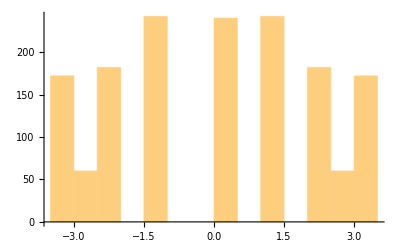

```mathematica
Histogram[Chop[Transpose[Simplify[angleinfo]][[2]]]]
```

```mathematica
OmegaTable={};
For[i=1,i<=Length[omegatable],i++,
(*Print[i];*)
om=omegatable[[i]];
link=om[[2]];
patch1=Select[SiteOwnerTable,#[[1]]==link[[1]]&][[1,2]];
patch2=Select[SiteOwnerTable,#[[1]]==link[[2]]&][[1,2]];
ω=om[[3]];

If[Length[OmegaTable]!=0,
If[
MemberQ[Transpose[OmegaTable][[1]],link],
Continue[];
];
];

If[patch1!=om[[1]],
s1=Select[coordinateChangeTable,#[[1]]==patch1&&#[[2]]==om[[1]]&&#[[3]]==link[[1]]&];
s2=Select[coordinateChangeTable,#[[2]]==patch1&&#[[1]]==om[[1]]&&#[[3]]==link[[1]]&];
If[Length[s1]==0&&Length[s2]==0,
Print["1!",patch1,patch2,om[[1]],link[[1]]];
Continue[];
];
If[Length[s1]!=0
,
ω+=s1[[1,4]];
,
Assert[Length[s2]!=0];
ω-=s2[[1,4]];
];
];

If[patch2!=om[[1]],
s1=Select[coordinateChangeTable,#[[1]]==patch2&&#[[2]]==om[[1]]&&#[[3]]==link[[2]]&];
s2=Select[coordinateChangeTable,#[[2]]==patch2&&#[[1]]==om[[1]]&&#[[3]]==link[[2]]&];
If[Length[s1]==0&&Length[s2]==0,
Print["2!"];
Continue[];
];
If[Length[s1]!=0
,
ω-=s1[[1,4]];
,
Assert[Length[s2]!=0];
ω+=s2[[1,4]];
];
];
AppendTo[OmegaTable,{om[[2]],ω}];
];

OmegaTable=Chop[Sort[OmegaTable]];
```

```mathematica
Angles={};
Do[
(*sitex=Sort[SiteOwnerTable][[ii]];*)
{ix,key}=sitex;
pos=Select[LinksInsideTables[key],#[[1]]==ix&];
neg=Select[LinksInsideTables[key],#[[2]]==ix&];

If[
Length[pos]!=0,
IsPos=1;
BaseLink=pos[[1]];
BaseLinkRow=GetRowNumbers[LinksInsideTables[key],BaseLink][[1]]
,
IsPos=0;
BaseLink=Reverse[neg[[1]]];
BaseLinkRow=GetRowNumbers[LinksInsideTables[key],Reverse[BaseLink]][[1]];
];

relativeangles=Select[angleinfo,
#[[1,1]]==BaseLink[[2]]&&#[[1,2]]==BaseLink[[1]]&
];

baseanglerelative=Select[relativeangles,
#[[1,1]]==BaseLink[[2]]&&#[[1,2]]==BaseLink[[1]]&&#[[1,3]]==BaseLink[[2]]&][[1,2]];

baseangle=(1-IsPos) Pi+alphaTables[key][[BaseLinkRow]][[2-IsPos]];

measuredangles={ix,#[[1,3]],Mod[#[[2]]+baseangle+baseanglerelative,2Pi,-Pi]}&/@relativeangles;
Angles=Join[Angles,measuredangles]
,
{sitex,SiteOwnerTable}
];
AlphaTable=Chop[{#[[1]],#[[2]],Chop[N[Mod[#[[3]],2Pi,-Pi]]]}&/@Angles];
```

```mathematica
(*check1*)
Do[
(*Print[ell];*)
pos=Select[AlphaTable,#[[1]]==ell[[1]]&&#[[2]]==ell[[2]]&];
neg=Select[AlphaTable,#[[2]]==ell[[1]]&&#[[1]]==ell[[2]]&];
om=Select[OmegaTable,#[[1,1]]==ell[[1]]&&#[[1,2]]==ell[[2]]&];

α1=pos[[1,3]];
α2=neg[[1,3]]+Pi;
ω=om[[1,2]];
(*Print[Mod[α1-(ω+α2),2Pi,-Pi]];*)
Assert[Abs[Mod[α1-(ω+α2),2Pi,-Pi]]<TOLSLOPPY]
,
{ell,AllLinks}
];
```

```mathematica
AllFaces=Flatten[Table[FacesInsideTables[key],{key,keys}],1];

(*check2*)
Do[
(*Print[f];*)
sel=Select[OmegaTable,MemberQ[f,#[[1,1]]]&&MemberQ[f,#[[1,2]]]&];
selα=Select[AlphaTable,MemberQ[f,#[[1]]]&&MemberQ[f,#[[2]]]&];

cross=Cross[PtsIcosahedron1P[[f[[2]]]]-PtsIcosahedron1P[[f[[1]]]],PtsIcosahedron1P[[f[[3]]]]-PtsIcosahedron1P[[f[[1]]]]];
mean=Mean[PtsIcosahedron1P[[#]]&/@f];
sign=Sign[cross.mean];

sum=0;
Do[
directedpair={f[[jj]],f[[Mod[jj+1,3,1]]]};
pos=Select[sel,#[[1]]==directedpair&];
neg=Select[sel,Reverse[#[[1]]]==directedpair&];

If[Length[pos]==1,
sum-=pos[[1,2]]
,
sum+=neg[[1,2]]
];

posα=Select[selα,{#[[1]],#[[2]]}==directedpair&][[1,3]];
negα=Select[selα,Reverse[{#[[1]],#[[2]]}]==directedpair&][[1,3]];
sum+=posα;
sum-=negα+Pi;
,
{jj,1,3}
];
Assert[IsModdable[sum,2.0Pi,TOLSLOPPY]]
,
{f,AllFaces}
];
```

```mathematica
omegaTable={#[[1,1]]-1,#[[1,2]]-1,#[[2]]}&/@OmegaTable;
SetDirectory[NotebookDirectory[]];
Export["omega_n"<>ToString[nrefine]<>".dat",omegaTable,"Table"]
```

omega_n2.dat

```mathematica
alphaTable={#[[1]]-1,#[[2]]-1,#[[3]]}&/@AlphaTable;
SetDirectory[NotebookDirectory[]];
Export["alpha_n"<>ToString[nrefine]<>".dat",alphaTable,"Table"]
```

alpha_n2.dat